## Setup

These are the parameters of our system. Everything is determined by , , , and .

```mathematica
(* Hyperexponential classes *)
(*mean11 = 1/100
mean12 =2
mean21 = 2
mean22 = 1/100
mean1 =0.99*mean11+0.01*mean12
mean2 = 0.99*mean21+0.01*mean22
S1Squared =0.99*(2*mean11^2)+0.01*(2*mean12^2)
S2Squared =0.99*(2*mean21^2)+0.01*(2*mean22^2)*)

(* Exponential sizes *)
mean1 =1
mean2 = 1/2
S1Squared =2*(mean1^2)
S2Squared =2*(mean2^2)

lambda1 = 0.45/mean1
lambda2 = 0.45/mean2
```

1

1/2

2

1/2

0.7

0.4

```mathematica
lambda = lambda1 + lambda2

rho1 =lambda1*mean1
rho2 = lambda2*mean2
rho = rho1 + rho2
```

1.1

0.7

0.2

0.9

```mathematica
S = lambda1/lambda*mean1 + lambda2/lambda*mean2
SSquared = (lambda1/lambda)*S1Squared + (lambda2/lambda*S2Squared)
excessS = SSquared/(2*S)
```

0.818182

1.45455

0.888889

## Non-Preemptive Analysis

We first consider the non-preemptive versions of the busy period and switching algorithms. See the overleaf doc for the theoretical analyses.

### Busy Period Algorithm

2.66667

10.

1.

26.6667

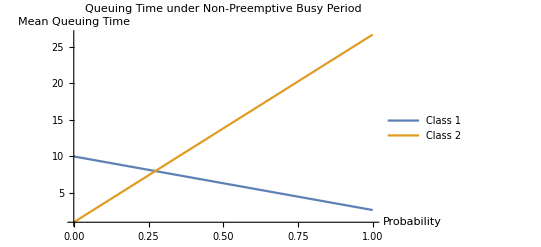

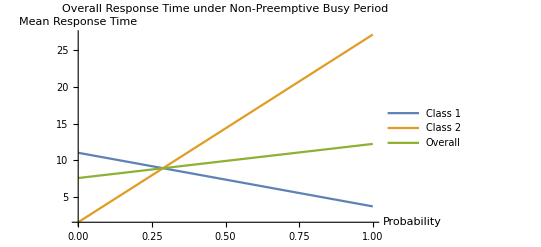

```mathematica
(* response time of class 1 if it has first priority *)
TQ1First = rho*excessS/(1-rho1)
(* response time of class 1 if it has second priority *)
TQ1Second = rho*excessS/((1-rho)(1-rho2))
(* response time of class 2 if it has first priority *)
TQ2First = rho*excessS/(1-rho2)
(* response time of class 2 if it has second priority *)
TQ2Second = rho*excessS/((1-rho)(1-rho1))

(* In BP, class 1 priority w.p. p, class 2 priority w.p. 1 - p *)
TQ1BP[p_] := p*TQ1First + (1-p)*TQ1Second
TQ2BP[p_] := p*TQ2Second + (1-p)*TQ2First

(* Overall response time is waiting time + size *)
T1BPNP[p_] := TQ1BP[p] + mean1
T2BPNP[p_] := TQ2BP[p] + mean2
TBPNP[p_] := (lambda1/lambda)*T1BPNP[p]+(lambda2/lambda)*T2BPNP[p]

Plot[{TQ1BP[p], TQ2BP[p]}, {p, 0, 1}, AxesLabel -> {"Probability", "Mean Queuing Time"}, PlotRange -> Full, PlotLegends -> {"Class 1", "Class 2"}, PlotLabel->"Queuing Time under Non-Preemptive Busy Period"]

Plot[{T1BPNP[p], T2BPNP[p], TBPNP[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Response Time"}, PlotRange -> Full, PlotLegends -> {"Class 1", "Class 2", "Overall"}, PlotLabel->"Overall Response Time under Non-Preemptive Busy Period"]
```

### Switching Algorithm

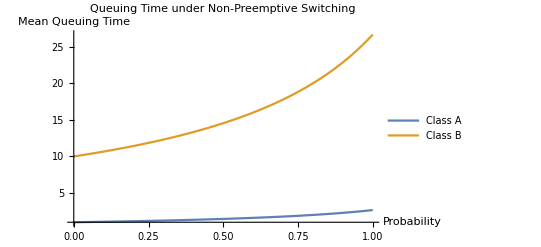

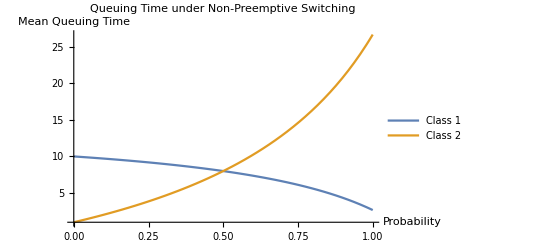

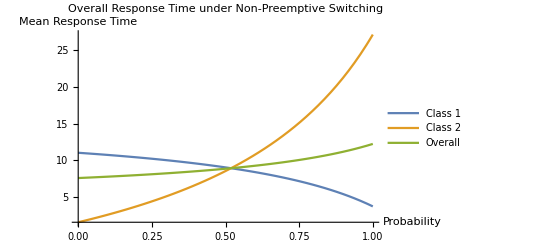

```mathematica
(* Setting up parameters *)
lambdaA[p_] := lambda1*p + lambda2*(1-p)
lambdaB[p_] := lambda2*p + lambda1 *(1-p)
meanSizeA[p_] := (p*rho1 + (1-p)*rho2)/lambdaA[p]
meanSizeB[p_] := (p*rho2 + (1-p)*rho1)/lambdaB[p]
meanSizeASquared[p_] := (p*lambda1*S1Squared + (1-p)*lambda2*S2Squared)/lambdaA[p]
meanSizeBSquared[p_]:= (p*lambda2*S2Squared + (1-p)*lambda1*S1Squared)/lambdaB[p]
rhoA[p_] := lambdaA[p]*meanSizeA[p]
rhoB[p_]:=lambdaB[p]*meanSizeB[p]

(* Mean response time for class A and class B *)
TQA[p_] := rho*excessS/(1-rhoA[p])
TQB[p_] := rho*excessS/((1-rhoA[p])(1-rho))
TQ1Switching[p_]:= p*TQA[p] + (1-p)*TQB[p]
TQ2Switching[p_] := p*TQB[p]+(1-p)*TQA[p]
T1OverallSwitching[p_]:=TQ1Switching[p] + mean1
T2OverallSwitching[p_] := TQ2Switching[p] + mean2
TOverallSwitching[p_] := (lambda1/lambda)*T1OverallSwitching[p]+(lambda2/lambda)*T2OverallSwitching[p]

Plot[{TQA[p], TQB[p]}, {p, 0, 1}, AxesLabel -> {"Probability", "Mean Queuing Time"}, PlotRange -> Full, PlotLegends -> {"Class A", "Class B"}, PlotLabel->"Queuing Time under Non-Preemptive Switching"]

Plot[{TQ1Switching[p], TQ2Switching[p]}, {p, 0, 1}, AxesLabel -> {"Probability", "Mean Queuing Time"}, PlotRange -> Full, PlotLegends -> {"Class 1", "Class 2"}, PlotLabel->"Queuing Time under Non-Preemptive Switching"]

Plot[{T1OverallSwitching[p], T2OverallSwitching[p], TOverallSwitching[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Response Time"}, PlotRange -> Full, PlotLegends -> {"Class 1", "Class 2", "Overall"}, PlotLabel->"Overall Response Time under Non-Preemptive Switching"]
```

### Comparing Switching and Busy Period

Lambda1: 0.7

Lambda2: 0.4

Lambda: 1.1

mean1:1

mean2:1/2

Rho1: 0.7

Rho2: 0.2

Rho: 0.9

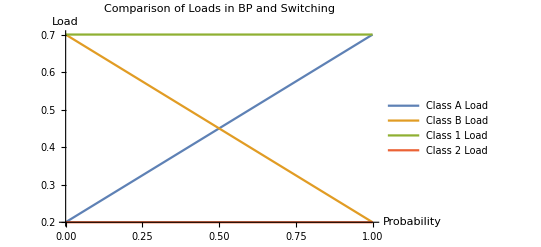

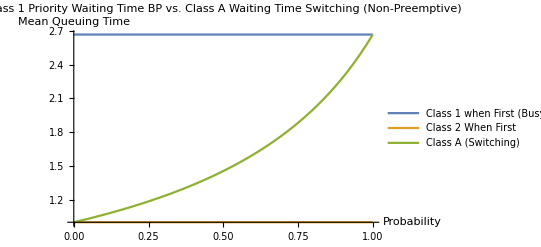

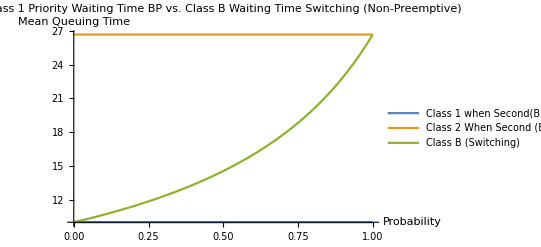

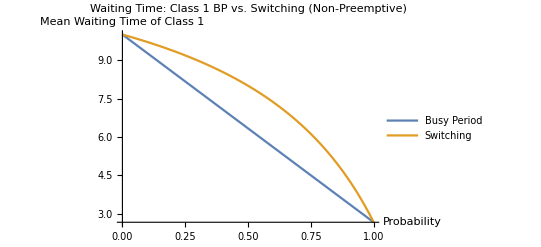

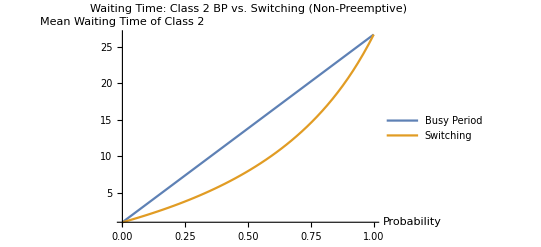

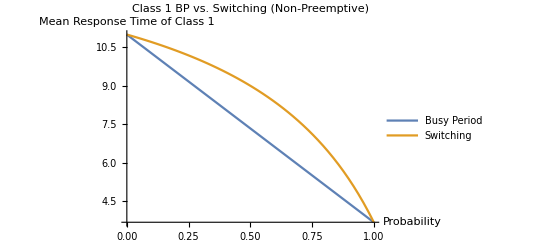

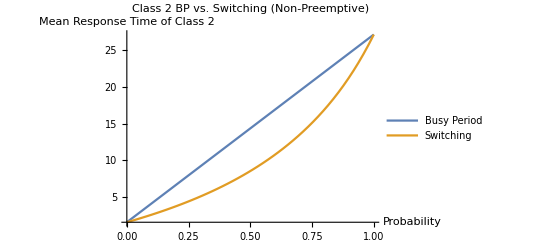

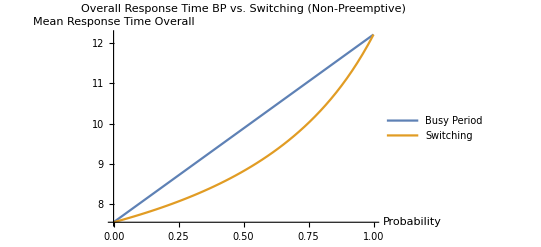

```mathematica
Print["Lambda1: ", lambda1]
Print["Lambda2: ", lambda2]
Print["Lambda: ", lambda]
(*Print["µ1: ", mu1]
Print["µ2: ", mu2]*)
Print["mean1:", mean1]
Print["mean2:", mean2]
Print["Rho1: ", rho1]
Print["Rho2: ", rho2]
Print["Rho: ", rho]

Plot[{rhoA[p],rhoB[p], rho1, rho2}, {p, 0, 1}, AxesLabel  -> {"Probability", "Load"}, PlotRange -> Full, PlotLegends -> {"Class A Load", "Class B Load", "Class 1 Load", "Class 2 Load"}, PlotLabel -> "Comparison of Loads in BP and Switching"]

Plot[{TQ1First, TQ2First, TQA[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Queuing Time"}, PlotRange -> Full, PlotLegends -> {"Class 1 when First (Busy Period)", "Class 2 When First", "Class A (Switching)"}, PlotLabel->"Class 1 Priority Waiting Time BP vs. Class A Waiting Time Switching (Non-Preemptive)"]
Plot[{TQ1Second, TQ2Second, TQB[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Queuing Time"}, PlotRange -> Full, PlotLegends -> {"Class 1 when Second(Busy Period)", "Class 2 When Second (Busy Period)", "Class B (Switching)"}, PlotLabel->"Class 1 Priority Waiting Time BP vs. Class B Waiting Time Switching (Non-Preemptive)"]

Plot[{TQ1BP[p], TQ1Switching[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Waiting Time of Class 1"}, PlotRange -> Full, PlotLegends -> {"Busy Period", "Switching"}, PlotLabel->"Waiting Time: Class 1 BP vs. Switching (Non-Preemptive)"]
Plot[{TQ2BP[p], TQ2Switching[p]}, {p, 0, 1}, AxesLabel -> {"Probability", "Mean Waiting Time of Class 2"}, PlotRange -> Full, PlotLegends -> {"Busy Period", "Switching"}, PlotLabel->"Waiting Time: Class 2 BP vs. Switching (Non-Preemptive)"]

Plot[{T1BPNP[p], T1OverallSwitching[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Response Time of Class 1"}, PlotRange -> Full, PlotLegends -> {"Busy Period", "Switching"}, PlotLabel->"Class 1 BP vs. Switching (Non-Preemptive)"]
Plot[{T2BPNP[p], T2OverallSwitching[p]}, {p, 0, 1}, AxesLabel -> {"Probability", "Mean Response Time of Class 2"}, PlotRange -> Full, PlotLegends -> {"Busy Period", "Switching"}, PlotLabel->"Class 2 BP vs. Switching (Non-Preemptive)"]
Plot[{TBPNP[p], TOverallSwitching[p]}, {p, 0, 1}, AxesLabel -> {"Probability", "Mean Response Time Overall"}, PlotRange -> Full, PlotLegends -> {"Busy Period", "Switching"}, PlotLabel->"Overall Response Time BP vs. Switching (Non-Preemptive)"]

Plot[{TQ1First, TQA[p], TQB[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Queuing Time"}, PlotRange -> Full, PlotLegends -> {"Class 1 when First(Busy Period)", "Class A (Switching)", "Class B (Switching)"}, PlotLabel->"Class 1 Priority Waiting Time BP vs. Class B Waiting Time Switching (Non-Preemptive)"]

Plot[{TQ1Second, TQA[p], TQB[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Queuing Time"}, PlotRange -> Full, PlotLegends -> {"Class 1 when Second(Busy Period)", "Class A (Switching)", "Class B (Switching)"}, PlotLabel->"Class 1 Priority Waiting Time BP vs. Class B Waiting Time Switching (Non-Preemptive)"]
```

### Mixing Time in Non-Preemptive Model

#### Switching Algorithm:

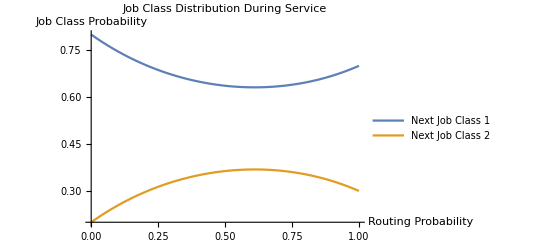

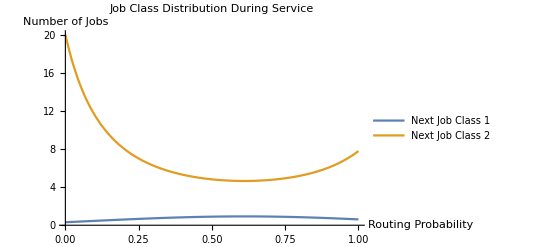

```mathematica
probNextJobClass1[p_] := rhoA[p]*(lambda1*p/lambdaA[p]) + (1-rhoA[p])*(lambda1*(1-p)/lambdaB[p])
(* Should be 1 - above, and is *)
probNextJobClass2[p_] := rhoA[p]*(lambda2*(1-p)/lambdaA[p]) + (1-rhoA[p])*(lambda2*p/lambdaB[p])

Plot[{probNextJobClass1[p], probNextJobClass2[p]}, {p, 0, 1},  AxesLabel->{"Routing Probability", "Job Class Probability"}, PlotRange -> Full, PlotLegends -> {"Next Job Class 1", "Next Job Class 2"}, PlotLabel->"Job Class Distribution During Service"]

(* This is distributed Geom(p') - 1, so variance is the same as geom(p') variance *)
numJobsBetweenClass1Jobs[p_] := (1-probNextJobClass1[p])/((probNextJobClass1[p])^2)
numJobsBetweenClass2Jobs[p_] := (1-probNextJobClass2[p])/((probNextJobClass2[p])^2)

Plot[{numJobsBetweenClass1Jobs[p], numJobsBetweenClass2Jobs[p]}, {p, 0, 1},  AxesLabel->{"Routing Probability", "Number of Jobs"}, PlotRange -> Full, PlotLegends -> {"Next Job Class 1", "Next Job Class 2"}, PlotLabel->"Job Class Distribution During Service"]
```

## Preemptive Analysis

Now we consider the same algorithms in the preemptive priority setting.

### Busy Period Algorithm

1

1/2

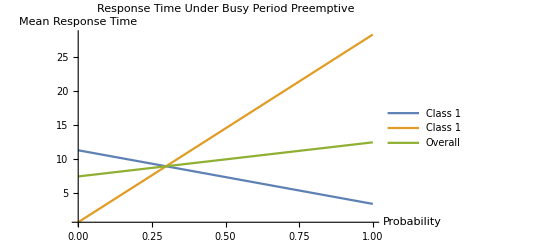

```mathematica
S1excess = S1Squared/(2*mean1)
S2excess = S2Squared/(2*mean2)
(* Response time of class 1 when first priority *)
T1First := mean1 + rho1*S1excess/(1-rho1)

(* Response time of class 1 when second priority *)
T1Second := mean1/(1-rho2) + rho*excessS/((1-rho)(1-rho2))

(* Response time of class 2 when first priority *)
T2First := mean2+ rho2*S2excess/(1-rho2)
(* Response time of class 2 when second priority *)
T2Second := mean2/(1-rho1) + rho*excessS/((1-rho)(1-rho1))

(* Overalls *)
T1BPPreemptive[p_] := p*T1First+(1-p)*T1Second
T2BPPreemptive[p_] := p*T2Second + (1-p)*T2First
TBPPreemptive[p_] := (lambda1/lambda)*T1BPPreemptive[p] + (lambda2/lambda)*T2BPPreemptive[p]

Plot[{T1BPPreemptive[p], T2BPPreemptive[p], TBPPreemptive[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Response Time"}, PlotRange -> Full, PlotLegends -> {"Class 1", "Class 1", "Overall"}, PlotLabel->"Response Time Under Busy Period Preemptive"]
```

### Switching Algorithm

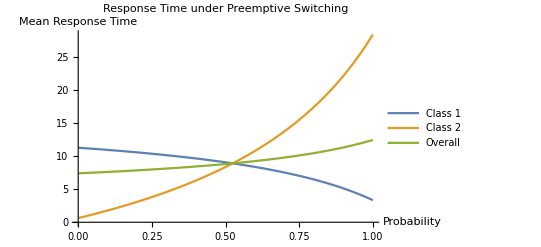

```mathematica
excessSA[p_] := meanSizeASquared[p]/(2*meanSizeA[p])
excessSB[p_] := meanSizeBSquared[p]/(2*meanSizeB[p])

(* Mean response time for class A job, given it's a class 1 or 2 job. The residence time depends on the size, but the waiting time does not *)
TAPreemptive1[p_] := mean1 + rhoA[p]*excessSA[p]/(1-rhoA[p])
TAPreemptive2[p_] := mean2 + rhoA[p]*excessSA[p]/(1-rhoA[p])

(* Same for class B job *)
TBPreemptive1[p_] := mean1/(1-rhoA[p]) + rho*excessS/((1-rho)(1-rhoA[p]))
TBPreemptive2[p_] := mean2/(1-rhoA[p]) + rho*excessS/((1-rho)(1-rhoA[p]))

T1SwitchingPreemptive[p_] := p*TAPreemptive1[p] + (1-p)*TBPreemptive1[p]
T2SwitchingPreemptive[p_]:= p*TBPreemptive2[p] + (1-p)*TAPreemptive2[p]
TOverallSwitchingPreemptive[p_] := (lambda1/lambda)*T1SwitchingPreemptive[p]+(lambda2/lambda)*T2SwitchingPreemptive[p]

Plot[{T1SwitchingPreemptive[p], T2SwitchingPreemptive[p], TOverallSwitchingPreemptive[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Response Time"}, PlotRange -> Full, PlotLegends -> {"Class 1", "Class 2", "Overall"}, AxesOrigin->{0,0}, PlotLabel->"Response Time under Preemptive Switching"]
```

### Comparing Busy Period and Switching in Preemptive Case

Lambda1: 0.7

Lambda2: 0.4

Lambda: 1.1

µ1: mu1

µ2: mu2

mean1:1

mean2:1/2

Rho1: 0.7

Rho2: 0.2

Rho: 0.9

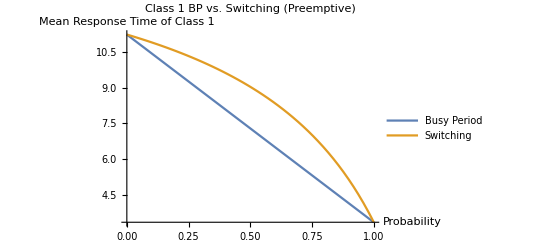

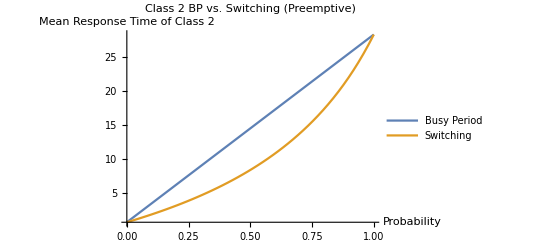

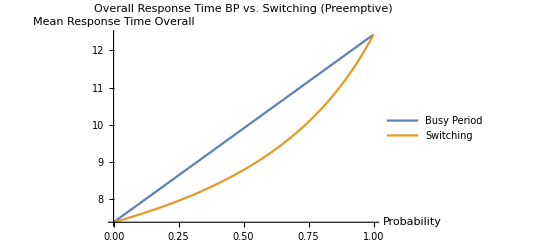

```mathematica
Print["Lambda1: ", lambda1]
Print["Lambda2: ", lambda2]
Print["Lambda: ", lambda]
Print["µ1: ", mu1]
Print["µ2: ", mu2]
Print["mean1:", mean1]
Print["mean2:", mean2]
Print["Rho1: ", rho1]
Print["Rho2: ", rho2]
Print["Rho: ", rho]
Plot[{T1BPPreemptive[p], T1SwitchingPreemptive[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Response Time of Class 1"}, PlotRange -> Full, PlotLegends -> {"Busy Period", "Switching"}, PlotLabel->"Class 1 BP vs. Switching (Preemptive)"]
Plot[{T2BPPreemptive[p], T2SwitchingPreemptive[p]}, {p, 0, 1}, AxesLabel -> {"Probability", "Mean Response Time of Class 2"}, PlotRange -> Full, PlotLegends -> {"Busy Period", "Switching"}, PlotLabel->"Class 2 BP vs. Switching (Preemptive)"]
Plot[{TBPPreemptive[p], TOverallSwitchingPreemptive[p]}, {p, 0, 1}, AxesLabel -> {"Probability", "Mean Response Time Overall"}, PlotRange -> Full, PlotLegends -> {"Busy Period", "Switching"}, PlotLabel->"Overall Response Time BP vs. Switching (Preemptive)"]
```

## Comparing Preemptive And Non-Preemptive

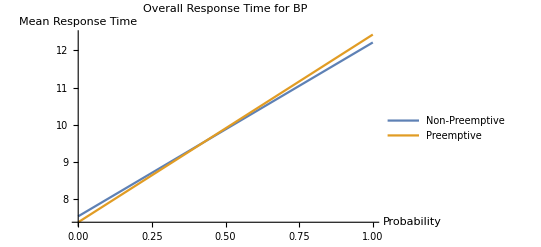

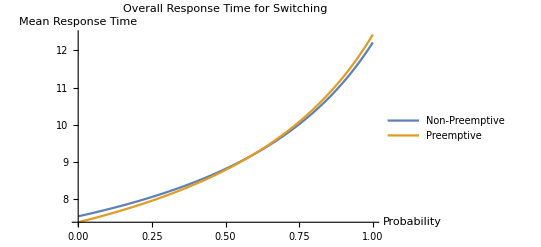

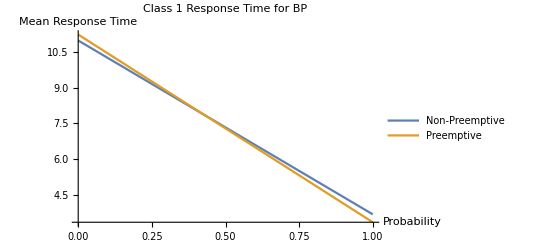

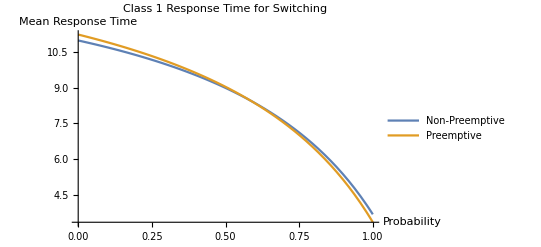

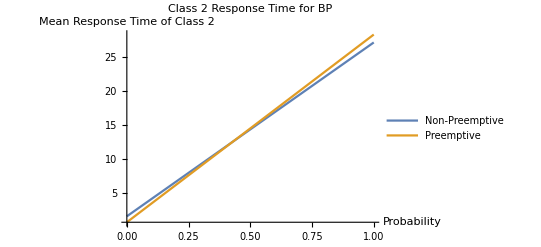

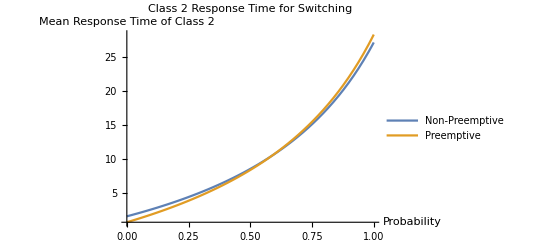

```mathematica
Plot[{TBPNP[p], TBPPreemptive[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Response Time"}, PlotRange -> Full, PlotLegends -> {"Non-Preemptive", "Preemptive"}, PlotLabel->"Overall Response Time for BP"]
Plot[{TOverallSwitching[p], TOverallSwitchingPreemptive[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Response Time"}, PlotRange -> Full, PlotLegends -> {"Non-Preemptive", "Preemptive"}, PlotLabel->"Overall Response Time for Switching"]
Plot[{T1BPNP[p], T1BPPreemptive[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Response Time"}, PlotRange -> Full, PlotLegends -> {"Non-Preemptive", "Preemptive"}, PlotLabel->"Class 1 Response Time for BP"]
Plot[{T1OverallSwitching[p], T1SwitchingPreemptive[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Response Time"}, PlotRange -> Full, PlotLegends -> {"Non-Preemptive", "Preemptive"}, PlotLabel->"Class 1 Response Time for Switching"]
Plot[{T2BPNP[p], T2BPPreemptive[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Response Time of Class 2"}, PlotRange -> Full, PlotLegends -> {"Non-Preemptive", "Preemptive"}, PlotLabel->"Class 2 Response Time for BP"]
Plot[{T2OverallSwitching[p], T2SwitchingPreemptive[p]}, {p, 0, 1}, AxesLabel->{"Probability", "Mean Response Time of Class 2"}, PlotRange -> Full, PlotLegends -> {"Non-Preemptive", "Preemptive"}, PlotLabel->"Class 2 Response Time for Switching"]
```